```mathematica
sineGaussian=A*Exp[-Γ*t^2]*Sin[2*π*Subscript[f, c]*t]
```

A ⅇ^(-t^2 Γ) Sin[2 π t f_c]

```mathematica
FT=Integrate[sineGaussian*Exp[2*π*f*I*t],{t,0,T}]
```

1/(4 √Γ)A ⅇ^(-(π^2 (f+f_c)^2)/Γ) √π (Erfi[(π (f+f_c))/(√Γ)]+ⅇ^((4 f π^2 f_c)/Γ) (-Erfi[(π (f-f_c))/(√Γ)]+Erfi[(f π+ⅈ T Γ-π f_c)/(√Γ)])-Erfi[(f π+ⅈ T Γ+π f_c)/(√Γ)])

```mathematica
T=1
```

1

```mathematica
Subscript[f, c]=30
```

30

```mathematica
Q=1
```

1

```mathematica
Γ=(2*π*Subscript[f, c])/Q
```

60 π

```mathematica
A=100
```

100

```mathematica
sineGaussian=A*Exp[-Γ*t^2]*Sin[2*π*Subscript[f, c]*t]
```

100 ⅇ^(-60 π t^2) Sin[60 π t]

```mathematica
FT=Integrate[sineGaussian*Exp[2*π*f*I*t],{t,0,T}]
```

-5/2 √(5/3) ⅇ^(-1/60 (30+f)^2 π) (ⅇ^(2 f π) (Erfi[1/2 (-30+f) √(π/15)]-Erfi[1/2 ((-30+60 ⅈ)+f) √(π/15)])-Erfi[1/2 (30+f) √(π/15)]+Erfi[1/2 ((30+60 ⅈ)+f) √(π/15)])

General::munfl: Exp[-753.921] is too small to represent as a normalized machine number; precision may be lost.

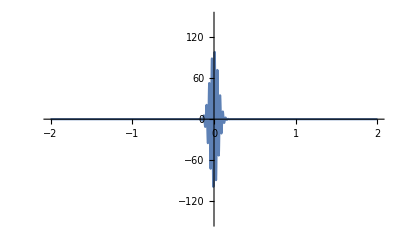

```mathematica
Plot[sineGaussian,{t,-2,2},PlotRange->{-150,150}]
```

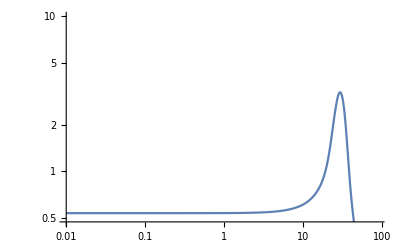

```mathematica
LogLogPlot[Abs[FT],{f,0.01,100},PlotRange->{0,10}]
```

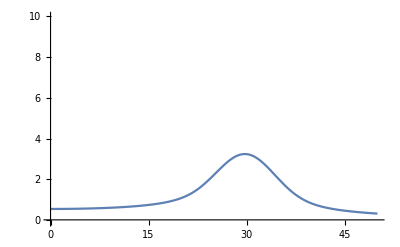

```mathematica
Plot[Abs[FT],{f,0,50},PlotRange->{-0.1,10}]
```

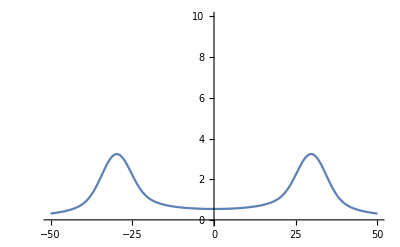

```mathematica
Plot[Abs[FT],{f,-50,50},PlotRange->{-0.1,10}]
```

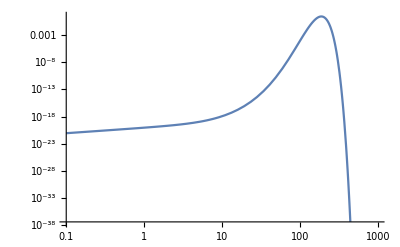

```mathematica
LogLogPlot[Abs[FourierTransform[sineGaussian,t,ω]],{ω,0.1,1000}]
```